# Problema 2.26

## Datos

```mathematica
(*in*)
d2=1.9;
d3=1.45;
d3p=2.3;
d5=2;(*Se modifico, es decir se aumento su logitud*)
```

## Ecuaciones cinemáticas

```mathematica
Clear[θ2,θ3,xb,θ5,xa]
Clear[ω2,ω3,vxb,ω5,vxa]
Clear[α2,α3,axb,α5,axa]
```

### Ecuaciones de Posición

```mathematica
u2={Cos[θ2],Sin[θ2],0};
u3={Cos[θ3],Sin[θ3],0};
u3p={Cos[θ3+(136.74*Degree)],Sin[θ3+(136.74*Degree)],0};(*Suma de angulos Theta y Betha*)
u5={Cos[θ5],Sin[θ5],0};

RL1={0,-1,0};
RL2={0,0.5,0};
R2=d2*u2;
R3=d3*u3;
R3p=d3p*u3p;
R5=d5*u5;
Ra={-xa,0,0};
Rb={-xb,0,0};

(*Lazos vectoriales*)

pos1=RL1+Rb+R5+R3p-Ra-RL2;
pos2=RL1+Rb+R5+R3-R2;
```

### Ecuaciones de Velocidad

```mathematica
omega2={0,0,ω2};
omega3={0,0,ω3};
omega5={0,0,ω5};

(*VL1={0,0,0},
VL2={0,0,0}, ambos son vectores nulos en velocidad*)
V2=omega2×R2;
V3=omega3×R3;
V3p=omega3×R3p;
V5=omega5×R5;
Va={-vxa,0,0};
Vb={-vxb,0,0};

(*Lazos vectoriales *)

vel1=Vb+V5+V3p-Va;
vel2=Vb+V5+V3-V2;
```

### Ecuaciones de Aceleración

```mathematica
alfa2={0,0,α2};
alfa3={0,0,α3};
alfa5={0,0,α5};

(*Definiendo vectores*)
A2=alfa2×R2-ω2^2*R2;
A3=alfa3×R3-ω3^2*R3;
A3p=alfa3×R3p-ω3^2*R3p;
A5=alfa5×R5-ω5^2*R5;
Aa={-axa,0,0};
Ab={-axb,0,0};

(*Lazos vectoriales *)

acel1=Ab+A5+A3p-Aa;
acel2=Ab+A5+A3-A2;
```

## Solución de Posición

```mathematica
Clear[θ2,θ3,xb,θ5,xa]
Clear[ω2,ω3,vxb,ω5,vxa]
Clear[α2,α3,axb,α5,axa]

θ2=157.5*Degree;(*Inicial*)

SolInicial = FindRoot[{
pos1⟦1⟧==0,
pos1⟦2⟧==0,
pos2⟦1⟧==0,
pos2⟦2⟧==0}, 
{{xa,5},
{xb,2.5},
{θ3,30*Degree},
{θ5,115*Degree}},MaxIterations->15]
```

{xa→5.24799,xb→1.26796,θ3→0.532086,θ5→2.62291}

### Solución Total (*Toda la vuelta*)

```mathematica
Clear[θ2,θ3,xb,θ5,xa]
Clear[ω2,ω3,vxb,ω5,vxa]
Clear[α2,α3,axb,α5,axa]
```

```mathematica
xai=xa/.SolInicial;  (*Tomando mis valores iniciales*)
xbi=xb/.SolInicial;
θ3i=θ3/.SolInicial;
θ5i=θ5/.SolInicial;

For[i = 1575,i≤5175, i+=10,
θ2=(i/10)*Degree;
SolPos[i]= FindRoot[{
pos1⟦1⟧==0,
pos1⟦2⟧==0,
pos2⟦1⟧==0,
pos2⟦2⟧==0}, 
{{xa,xai},
{xb,xbi},
{θ3,θ3i},
{θ5,θ5i}},MaxIterations->15];

xai=xa/.SolPos[i];
xbi=xb/.SolPos[i];
θ3i=θ3/.SolPos[i];
θ5i=θ5/.SolPos[i];]

?SolPos;
```

## Gráficas de posición

```mathematica
tabla1 = Table[{i/10,xa/.SolPos[i]},{i,1575,5175,10}];
tabla2 = Table[{i/10,xb/.SolPos[i]},{i,1575,5175,10}];
tabla3 = Table[{i/10,(θ3/.SolPos[i])/Degree},{i,1575,5175,10}];
tabla4 = Table[{i/10,(θ5/.SolPos[i])/Degree},{i,1575,5175,10}];
```

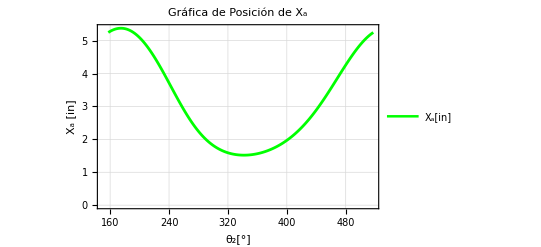

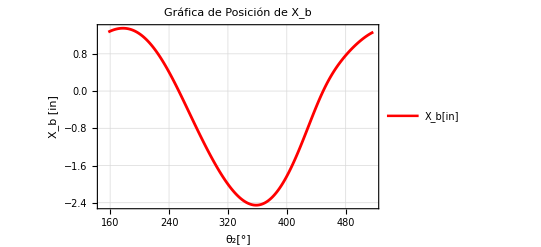

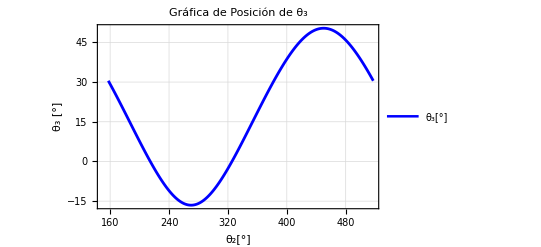

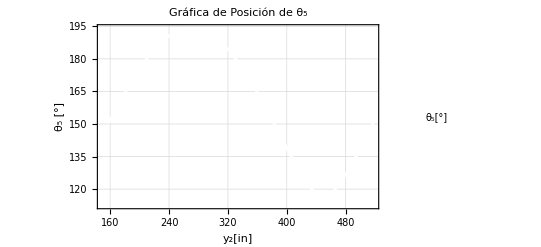

```mathematica
ListPlot[tabla1,
Frame->True,
FrameLabel->{"θ_2[°]","X_a [in]"},
PlotLabel->"Gráfica de Posición de X_a",
PlotLegends->{"X_a[in]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{Green,Thickness[0.005]},
ImageSize->400]


ListPlot[tabla2,
Frame->True,
FrameLabel->{"θ_2[°]","X_b [in]"},
PlotLabel->"Gráfica de Posición de X_b",
PlotLegends->{"X_b[in]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{Red,Thickness[0.005]},
ImageSize->400]


ListPlot[tabla3,
Frame->True,
FrameLabel->{"θ_2[°]","θ_3 [°]"},
PlotLabel->"Gráfica de Posición de θ_3",
PlotLegends->{"θ_3[°]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{Blue,Thickness[0.005]},
ImageSize->400]


ListPlot[tabla4,
Frame->True,
FrameLabel->{"y_2[in]","θ_5 [°]"},
PlotLabel->"Gráfica de Posición de θ_5",
PlotLegends->{"θ_5[°]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{White,Thickness[0.005]},
ImageSize->400]
```

## Solución de Velocidad

```mathematica
Clear[θ2,θ3,xb,θ5,xa]
Clear[ω2,ω3,vxb,ω5,vxa]
Clear[α2,α3,axb,α5,axa]

ω2=-1; (*rad/s y sentido horario*)

For[i = 1575,i≤5175, i+=10,
θ2=(i/10)*Degree;

SolVel[i]=Solve[{
vel1⟦1⟧==0,
vel1⟦2⟧==0,
vel2⟦1⟧==0,
vel2⟦2⟧==0}/.SolPos[i],
{vxa,vxb,ω3,ω5}]//Flatten;];
```

## Gráficas de Velocidad

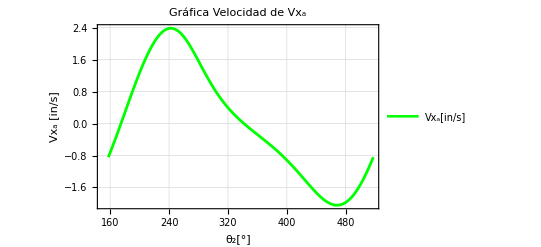

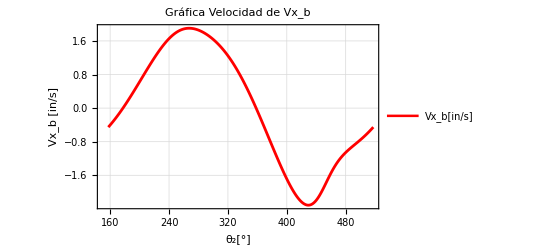

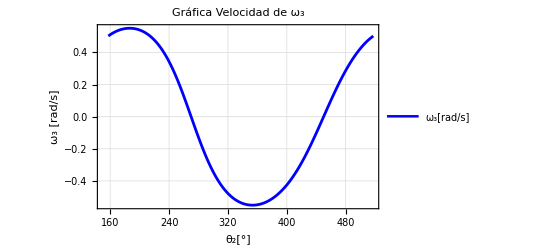

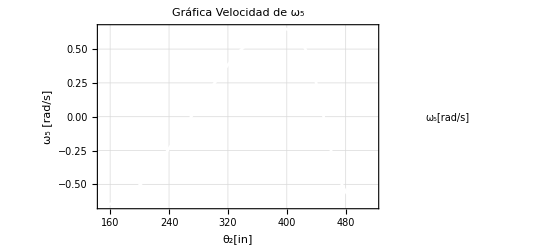

```mathematica
tabla5=Table[{i/10,vxa/.SolVel[i]},{i,1575,5175,10}];
tabla6=Table[{i/10,vxb/.SolVel[i]},{i,1575,5175,10}];
tabla7=Table[{i/10,ω3/.SolVel[i]},{i,1575,5175,10}];
tabla8=Table[{i/10,ω5/.SolVel[i]},{i,1575,5175,10}];

ListPlot[tabla5,
Frame->True,
FrameLabel->{"θ_2[°]","Vx_a [in/s]"},
PlotLabel->"Gráfica Velocidad de Vx_a",
PlotLegends->{"Vx_a[in/s]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{Green,Thickness[0.005]},
ImageSize->400]


ListPlot[tabla6,
Frame->True,
FrameLabel->{"θ_2[°]","Vx_b [in/s]"},
PlotLabel->"Gráfica Velocidad de Vx_b",
PlotLegends->{"Vx_b[in/s]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{Red,Thickness[0.005]},
ImageSize->400]


ListPlot[tabla7,
Frame->True,
FrameLabel->{"θ_2[°]","ω_3 [rad/s]"},
PlotLabel->"Gráfica Velocidad de ω_3",
PlotLegends->{"ω_3[rad/s]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{Blue,Thickness[0.005]},
ImageSize->400]


ListPlot[tabla8,
Frame->True,
FrameLabel->{"θ_2[in]","ω_5 [rad/s]"},
PlotLabel->"Gráfica Velocidad de ω_5",
PlotLegends->{"ω_5[rad/s]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{White,Thickness[0.005]},
ImageSize->400]
```

## Solución de Aceleración

```mathematica
Clear[θ2,θ3,xb,θ5,xa]
Clear[ω2,ω3,vxb,ω5,vxa]
Clear[α2,α3,axb,α5,axa]

ω2=-1; 
α2=0; 

For[i = 1575,i≤5175, i+=10,
θ2=i*Degree;

SolAcel[i]= Solve[{
acel1⟦1⟧==0,
acel1⟦2⟧==0,
acel2⟦1⟧==0,
acel2⟦2⟧==0}/.SolVel[i]/.SolPos[i] ,
{axa,axb,α3,α5}]//Flatten;];
```

## Gráficas Aceleración

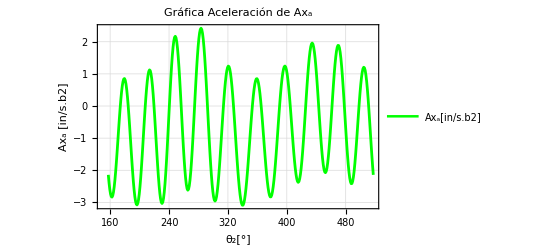

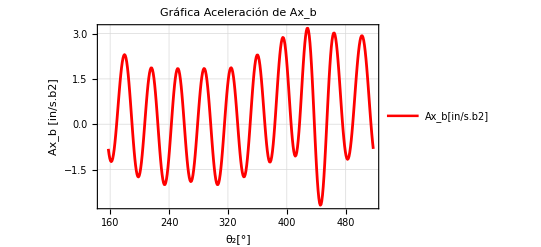

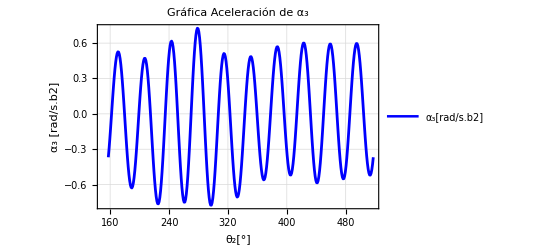

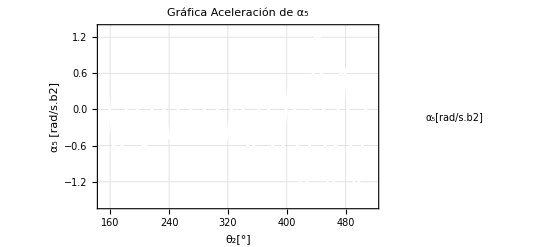

```mathematica
tabla9= Table[{i/10,axa/.SolAcel[i]},{i,1575,5175,10}];
tabla10= Table[{i/10,axb/.SolAcel[i]},{i,1575,5175,10}];
tabla11= Table[{i/10,α3/.SolAcel[i]},{i,1575,5175,10}];
tabla12= Table[{i/10,α5/.SolAcel[i]},{i,1575,5175,10}];

ListPlot[tabla9,
Frame->True,
FrameLabel->{"θ_2[°]","Ax_a [in/s.b2]"},
PlotLabel->"Gráfica Aceleración de Ax_a",
PlotLegends->{"Ax_a[in/s.b2]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{Green,Thickness[0.005]},
ImageSize->400]


ListPlot[tabla10,
Frame->True,
FrameLabel->{"θ_2[°]","Ax_b [in/s.b2]"},
PlotLabel->"Gráfica Aceleración de Ax_b",
PlotLegends->{"Ax_b[in/s.b2]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{Red,Thickness[0.005]},
ImageSize->400]


ListPlot[tabla11,
Frame->True,
FrameLabel->{"θ_2[°]","α_3 [rad/s.b2]"},
PlotLabel->"Gráfica Aceleración de α_3",
PlotLegends->{"α_3[rad/s.b2]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{Blue,Thickness[0.005]},
ImageSize->400]


ListPlot[tabla12,
Frame->True,
FrameLabel->{"θ_2[°]","α_5 [rad/s.b2]"},
PlotLabel->"Gráfica Aceleración de α_5",
PlotLegends->{"α_5[rad/s.b2]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{White,Thickness[0.005]},
ImageSize->400]
```

## Simulación

```mathematica
Clear[θ2,θ3,xb,θ5,xa]
```

```mathematica
Animate[

θ2=(i/10)*Degree;
x={1,0,0};
k={0,0,1};
cero={0,0,0};

eslabon2=Cylinder[{cero,R2},0.1];
eslabon3a=Cylinder[{R2+0.4*k,R2-R3+0.4*k},0.1]/.SolPos[i];
eslabon3b=Cylinder[{R2-R3+0.4*k,R2-R3+R3p+0.4*k},0.1]/.SolPos[i];
eslabon3c=Cylinder[{R2+0.4*k,R2-R3+R3p+0.4*k},0.1]/.SolPos[i];
eslabon4=Cylinder[{RL1+Rb-0.4*x+0.7*k,RL1+Rb+0.4*x+0.7*k},0.2]/.SolPos[i];
eslabon5=Cylinder[{RL1+Rb+0.7*k,RL1+Rb+R5+0.7*k},0.1]/.SolPos[i];
eslabon6=Cylinder[{R2-R3+R3p-0.4*x+0.4*k,R2-R3+R3p+0.4*x+0.4*k},0.2]/.SolPos[i];

ejeA=Cylinder[{R2-R3+R3p+0.2*k,R2-R3+R3p+0.6*k},0.15]/.SolPos[i];
ejeB=Cylinder[{RL1+Rb+0.5*k,RL1+Rb+0.9*k},0.15]/.SolPos[i];
ejeC=Cylinder[{R2-R3+0.3k,R2-R3+0.8*k},0.15]/.SolPos[i];
ejeD=Cylinder[{R2-0.2*k,R2+0.5*k},0.15];
ejeE=Cylinder[{-0.2*k,0.2*k},0.15];

barra2=Graphics3D[{Purple,eslabon2}];
barra3a=Graphics3D[{Green,eslabon3a}];
barra3b=Graphics3D[{Green,eslabon3b}];
barra3c=Graphics3D[{Green,eslabon3c}];
corredera4=Graphics3D[{Yellow,eslabon4}];
barra5=Graphics3D[{Red,eslabon5}];
corredera6=Graphics3D[{Orange,eslabon6}];

pernoA=Graphics3D[{Black,ejeA}];
pernoB=Graphics3D[{Black,ejeB}];
pernoC=Graphics3D[{Black,ejeC}];
pernoD=Graphics3D[{Black,ejeD}];
pernoE=Graphics3D[{Black,ejeE}];

Show[barra2,barra3a,barra3b,barra3c,corredera4,barra5,corredera6,pernoA,pernoB,pernoC,pernoD,pernoE,
Axes->True,
AxesLabel->{"X [in]","Y [in]","Z [in]"},
ImageSize->400,
ViewVertical->{0,1,0},
ViewPoint->{0,0,Infinity},
PlotRange->{{-7,4},{-3,2},{-1,1.3}}
],{i,1575,5175,10},AnimationRunning->False]
```